```mathematica
list = Import[NotebookDirectory[]<>"/res/out_0.0_2.0.txt","Table"];
Length[list]
len=Length[list[[1]]]
```

50

201

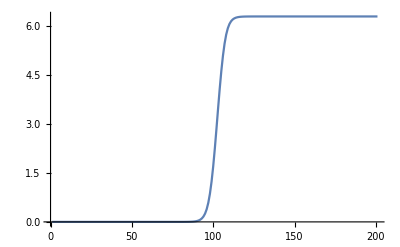

```mathematica
ListLinePlot[list[[10]],PlotRange->All]
```

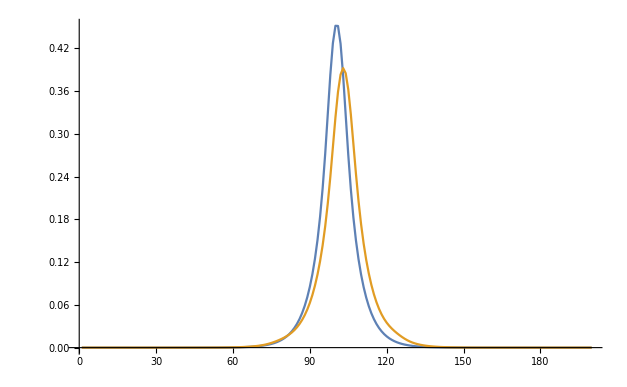

```mathematica
ListLinePlot[{Differences[list[[1]]],Differences[list[[-1]]]},PlotRange->Full]
```

```mathematica
f1=NIntegrate[Interpolation[Differences[list[[1]]]^2,InterpolationOrder->2][x],{x,1,len-1}]
f2=NIntegrate[Interpolation[Differences[list[[-1]]]^2,InterpolationOrder->2][x],{x,1,len-1}]
(f2-f1)/f1
```

2.83244

2.48369

-0.123124